```mathematica
μ=0;
σ=1;
num=100000;
pdf[x_]=PDF[NormalDistribution[μ,σ],x];
cdf[x_]=CDF[NormalDistribution[μ,σ],x];
cdfi[a_]=Solve[cdf[x]==a,x][[1,1,2]];
data=cdfi[a]/.a->RandomReal[{0,1},num];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

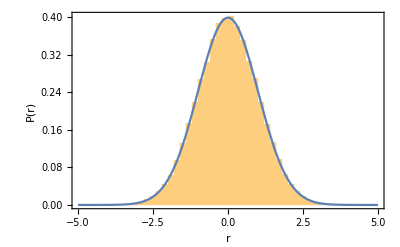

gauss.pdf

```mathematica
xmin=-5;
xmax=5;
p1=Histogram[data,50,"PDF"];
p2=Plot[pdf[x],{x,xmin,xmax},PlotRange->{{xmin,xmax},All}];
p3=Show[p1,p2,Frame->{{True,False},{True,False}},FrameLabel->{"r","P(r)"},FrameStyle->15,PlotRange->{{xmin,xmax},All}]
Export["gauss.pdf",p3]
```